# Data generation

## TODO

## Data format

### general information

Artificial data generation for clulstering varidity.

Data structire:
<Model and annotation>
;
<Dimension>[\tab]<Number of clusters>[\tab]<Number of samples>[\tab]<Number of background points>
;
<Cluster centers (model): matrix with tab delimiter>
;
<Samples: matrix with tab delimiter>
;

### answer form

< x1 >[\tab]< y2 >[\tab]...[\tab]<cl1>
< x2 >[\tab]< y2 >[\tab]...[\tab]<cl2>
...

## Preparation

```mathematica
(*dir="/Users/amanokou/gitsrc/"*)
```

```mathematica
dir="/home/kamano/gitsrc/"
```

/home/kamano/gitsrc/

```mathematica
(*dir="/Users/kouamano/gitsrc/"*)
```

```mathematica
Get[dir<>"MATH_SCRIPT/SCRIPTS/polar.txt"]
```

```mathematica
SetDirectory[dir<>"ClusteringAdequation/generative-data"]
```

/home/kamano/gitsrc/ClusteringAdequation/generative-data

## Programs

```mathematica
strDataToExportStr[n_]:=StringJoin[Riffle[{anntS[n],dimS[n],centersS[n],samplesS[n]},";\n"]]
```

```mathematica
distanceMat[mat_]:=Module[
{n},
n=Length[mat];
Table[EuclideanDistance[mat[[i]],mat[[j]]],{i,n},{j,n}]
]
```

## 2D

### data 1 (general)

```mathematica
id=1
```

1

```mathematica
anntS[id]="Model: central random, circles, one radius, triangle.\n"
```

Model: central random, circles, one radius, triangle.

```mathematica
dim[id]=2;
numClass[id]=3;
numSample[id]={100,100,100};
numBG[id]={0};
```

```mathematica
dimS[id]=StringJoin[Riffle[{ToString[dim[id]],ToString[numClass[id]],ToString[numSample[id]],ToString[numBG[id]]},"\t"],"\n"]
```

2	3	{100, 100, 100}	{0}

```mathematica
centers[id]=Map[polarToxy[N[{1,#}]]&,Table[2Pi/numClass[id] n,{n,0,2}]]
```

{{1.,0.},{-0.5,0.866025},{-0.5,-0.866025}}

```mathematica
centersS[id]=ExportString[centers[id],"TSV"]<>"\n"
```

1.	0.
-0.4999999999999998	0.8660254037844387
-0.5000000000000004	-0.8660254037844384

```mathematica
distanceMat[centers[id]]
```

{{0.,1.73205,1.73205},{1.73205,0.,1.73205},{1.73205,1.73205,0.}}

```mathematica
distMean[id]=Tr[Flatten[distanceMat[centers[id]]]]/(numClass[id]^2-numClass[id])
```

1.73205

```mathematica
samples[id]=Table[Map[#+centers[id][[n]]&,Table[polarToxy[{RandomReal[{0,distMean[id]/2.5}],RandomReal[{0,2Pi}]}],{numSample[id][[n]]}]],{n,numClass[id]}];
```

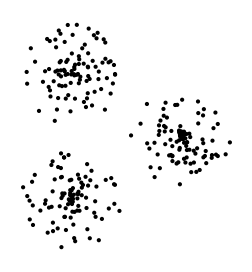

```mathematica
Graphics[Map[Point[#]&,samples[id],{2}]]
```

```mathematica
samplesS[id]=ExportString[Flatten[samples[id],1],"TSV"]<>"\n";
```

正解データ

```mathematica
samplesWithCl[id]=Flatten[Table[Map[Append[#,i]&,samples[id][[i]]],{i,Length[samples[id]]}],1];
```

全サンプルの平均半径

```mathematica
totalCenter[id]=Mean[Flatten[samples[id],1]]
```

{0.0251239,0.00906088}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id],1]]]
```

1.05136

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id]]
```

{{1.03266,-0.0493119},{-0.450553,0.918764},{-0.506734,-0.84227}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{0.308055,0.362356,0.335292}

Export 4f iles:

```mathematica
Export["data1.tsv",strDataToExportStr[id],"String"]
```

data1.tsv

```mathematica
Export["data1.ans.tsv",samplesWithCl[id]]
```

tmp.tsv

```mathematica
Export["data1.ans.totalR",totalR[id],"Table"]
```

data1.ans.totalR

```mathematica
Export["data1.ans.clRs",clRs[id],"Table"]
```

data1.ans.clRs

### data 2 (unbalanced)

```mathematica
id=2
```

2

```mathematica
anntS[id]="Model: unbalanced central random, circles, radiuses.\n"
```

Model: unbalanced central random, circles, radiuses.

```mathematica
dim[id]=2;
numClass[id]=3;
numSample[id]={200,100,50};
numBG[id]={0};
```

```mathematica
dimS[id]=StringJoin[Riffle[{ToString[dim[id]],ToString[numClass[id]],ToString[numSample[id]],ToString[numBG[id]]},"\t"],"\n"]
```

2	3	{200, 100, 50}	{0}

```mathematica
centers[id]={{0,0},{0.5,-1},{-0.5,-0.75}}
```

{{0,0},{0.5,-1},{-0.5,-0.75}}

```mathematica
centersS[id]=ExportString[centers[id],"TSV"]<>"\n"
```

0	0
0.5	-1
-0.5	-0.75

```mathematica
distanceMat[centers[id]]
```

{{0,1.11803,0.901388},{1.11803,0.,1.03078},{0.901388,1.03078,0.}}

```mathematica
distMean[id]=Tr[Flatten[distanceMat[centers[id]]]]/(numClass[id]^2-numClass[id])
```

1.01673

```mathematica
radius[id]={distMean[id]*0.5,distMean[id]*0.35,distMean[id]*0.17}
```

{0.508366,0.355856,0.172845}

```mathematica
samples[id]=Table[Map[#+centers[id][[n]]&,Table[polarToxy[{RandomReal[{0,radius[id][[n]]}],RandomReal[{0,2Pi}]}],{numSample[id][[n]]}]],{n,numClass[id]}];
```

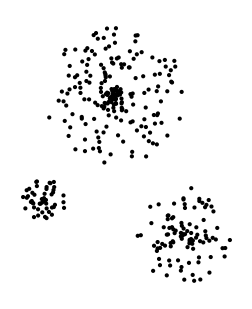

```mathematica
Graphics[Map[Point[#]&,samples[id],{2}]]
```

```mathematica
samplesS[id]=ExportString[Flatten[samples[id],1],"TSV"]<>"\n";
```

全サンプルの平均半径

```mathematica
id=2
```

2

```mathematica
totalCenter[id]=Mean[Flatten[samples[id],1]]
```

{0.0811993,-0.384752}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id],1]]]
```

0.585552

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id]]
```

{{0.0111856,0.0174839},{0.514901,-1.00858},{-0.50615,-0.746037}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{0.248668,0.181897,0.093187}

```mathematica
Export["data2.tsv",strDataToExportStr[2],"String"]
```

data2.tsv

```mathematica
Export["data2.ans.totalR",totalR[id],"Table"]
```

data2.ans.totalR

```mathematica
Export["data2.ans.clRs",clRs[id],"Table"]
```

data2.ans.clRs

### data 4 (sub class)

```mathematica
anntS[4]="Model: central random , circles, one radius, subclusters.\n"
```

Model: central random , circles, one radius, subclusters.

```mathematica
dim[4]=2;
numClass[4]=4;
numSample[4]={100,100,100,100};
numBG[4]={0};
```

```mathematica
dimS[4]=StringJoin[Riffle[{ToString[dim[4]],ToString[numClass[4]],ToString[numSample[4]],ToString[numBG[4]]},"\t"],"\n"]
```

2	4	{100, 100, 100, 100}	{0}

```mathematica
centers[4]={{2,1},{2,-1},{-2,1},{-2,-1}}
```

{{2,1},{2,-1},{-2,1},{-2,-1}}

```mathematica
centersS[4]=ExportString[centers[4],"TSV"]<>"\n"
```

2	1
2	-1
-2	1
-2	-1

```mathematica
distMean[4]=Tr[Flatten[distanceMat[centers[4]]//N]]/(numClass[4]^2-numClass[4])
```

3.49071

```mathematica
samples[4,"class"]=Table[Map[#+centers[4][[n]]&,Table[polarToxy[{RandomReal[{0,distMean[4]/4}],RandomReal[{0,2Pi}]}],{numSample[4][[n]]}]],{n,numClass[4]}];
```

```mathematica
maxmin[4]=Map[{Max[#],Min[#]}&,Transpose[Flatten[samples[4,"class"],1]]]
```

{{2.8547,-2.83024},{1.86456,-1.73736}}

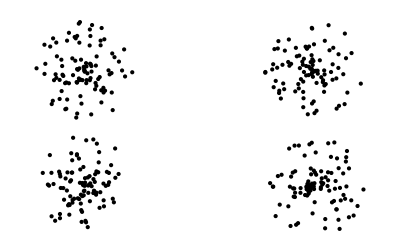

```mathematica
Graphics[Map[Point[#]&,Flatten[samples[4,"class"],1]]]
```

```mathematica
samplesS[4]=ExportString[Flatten[samples[4,"class"],1],"TSV"]<>"\n";
```

全サンプルの平均半径

```mathematica
id=4
```

4

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{-0.0271649,0.0205847}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

2.26297

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{1.91498,1.01336},{2.03195,-0.979934},{-2.02759,1.02384},{-2.02799,-0.974927}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{0.424125,0.433668,0.456422,0.398069}

```mathematica
Export["data4.tsv",strDataToExportStr[4],"String"]
```

data4.tsv

```mathematica
Export["data4.ans.totalR",totalR[id],"Table"]
```

data4.ans.totalR

```mathematica
Export["data4.ans.clRs",clRs[id],"Table"]
```

data4.ans.clRs

### data 5 (ring + disc)

```mathematica
anntS[5]="Model: central random , disc + ring.\n"
```

Model: central random , disc + ring.

```mathematica
dim[5]=2;
numClass[5]=2;
numSample[5]={100,200};
numBG[5]={0};
```

```mathematica
dimS[5]=StringJoin[Riffle[{ToString[dim[5]],ToString[numClass[5]],ToString[numSample[5]],ToString[numBG[5]]},"\t"],"\n"]
```

2	2	{100, 200}	{0}

```mathematica
centers[5]={{0,0},{0,0}}
```

{{0,0},{0,0}}

```mathematica
centersS[5]=ExportString[centers[5],"TSV"]<>"\n"
```

0	0
0	0

```mathematica
samples[5,"disc"]=Map[polarToxy[#]&,Table[{RandomReal[{0,1}],RandomReal[{0,2 Pi}]},{numSample[5][[1]]}]];
```

```mathematica
samples[5,"ring"]=Map[polarToxy[#]&,Table[{RandomReal[{1.5,2}],RandomReal[{0,2 Pi}]},{numSample[5][[2]]}]];
```

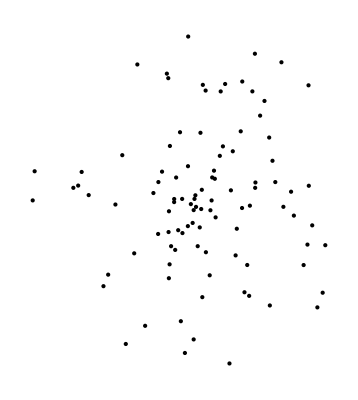

```mathematica
Graphics[Map[Point[#]&,samples[5,"disc"]]]
```

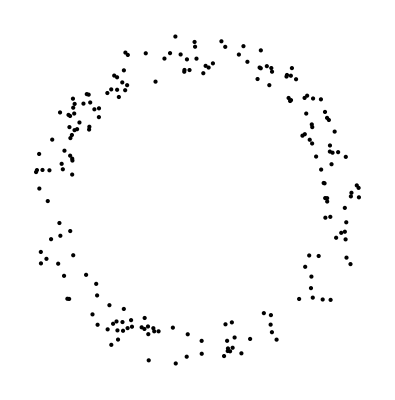

```mathematica
Graphics[Map[Point[#]&,samples[5,"ring"]]]
```

```mathematica
samples[5,"class"]=List[samples[5,"disc"],samples[5,"ring"]];
```

```mathematica
(*samplesS[1]=ExportString[Flatten[samples[1],1],"TSV"]<>"\n";*)
```

```mathematica
samplesS[5]=ExportString[Flatten[samples[5,"class"],1],"TSV"]<>"\n";
```

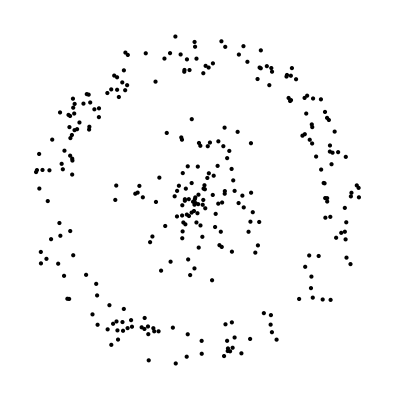

```mathematica
Map[Point[#]&,samples[5,"class"]]//Graphics
```

全サンプルの平均半径

```mathematica
id=5
```

5

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{0.0131921,0.115009}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

1.31454

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{0.055273,0.0229501},{-0.00784828,0.161038}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{0.47661,1.7249}

```mathematica
Export["data5.tsv",strDataToExportStr[5],"String"]
```

data5.tsv

```mathematica
Export["data5.ans.totalR",totalR[id],"Table"]
```

data5.ans.totalR

```mathematica
Export["data5.ans.clRs",clRs[id],"Table"]
```

data5.ans.clRs

### data 6 (spiral)

```mathematica
anntS[6]="Model: spiral x 3.\n"
```

Model: spiral x 3.

```mathematica
dim[6]=2;
numClass[6]=3;
numSample[6]={100,100,100};
numBG[6]={0};
```

```mathematica
dimS[6]=StringJoin[Riffle[{ToString[dim[6]],ToString[numClass[6]],ToString[numSample[6]],ToString[numBG[6]]},"\t"],"\n"]
```

2	3	{100, 100, 100}	{0}

```mathematica
origins[6]={{0,0},{0,0},{0,0}}
```

{{0,0},{0,0},{0,0}}

```mathematica
(samples[6,0]=Map[polarToxy[#]&,Table[{r,3r},{r,0.5,3-0.02,0.025}]])//Length
```

100

```mathematica
center[6,0]=Mean[samples[6,0]]
```

{0.0684864,0.339278}

```mathematica
(samples[6,1]=Map[polarToxy[#]&,Table[{r,3r+(2Pi/3)},{r,0.5,3-0.02,0.025}]])//Length
```

100

```mathematica
center[6,1]=Mean[samples[6,1]]
```

{-0.328066,-0.110328}

```mathematica
(samples[6,2]=Map[polarToxy[#]&,Table[{r,3r+(4Pi/3)},{r,0.5,3-0.02,0.025}]])//Length
```

100

```mathematica
center[6,2]=Mean[samples[6,2]]
```

{0.25958,-0.22895}

```mathematica
centers[6]={center[6,0],center[6,1],center[6,2]}
```

{{0.0684864,0.339278},{-0.328066,-0.110328},{0.25958,-0.22895}}

```mathematica
centersS[6]=ExportString[centers[6],"TSV"]<>"\n"
```

0.06848640517315346	0.3392778825308757
-0.3280664678005077	-0.11032797457161272
0.25958006262735384	-0.22894990795926298

```mathematica
samples[6,"class"]=List[samples[6,0],samples[6,1],samples[6,2]];
```

```mathematica
samplesS[6]=ExportString[Flatten[samples[6,"class"],1],"TSV"]<>"\n";
```

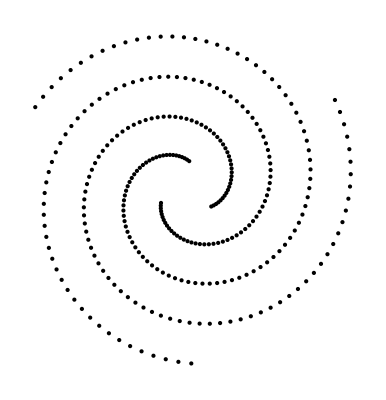

```mathematica
Map[Point[#]&,samples[6,"class"]]//Graphics
```

全サンプルの平均半径

```mathematica
id=6
```

6

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{-1.12503×10^-16,4.81097×10^-17}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

1.7375

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{0.0684864,0.339278},{-0.328066,-0.110328},{0.25958,-0.22895}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{1.71971,1.71971,1.71971}

```mathematica
Export["data6.tsv",strDataToExportStr[6],"String"]
```

data6.tsv

```mathematica
Export["data6.ans.totalR",totalR[id],"Table"]
```

data6.ans.totalR

```mathematica
Export["data6.ans.clRs",clRs[id],"Table"]
```

data6.ans.clRs

## Noisy

### data 3 (noisy)

```mathematica
anntS[3]="Model: central random + noise, circles, one radius, triangle.\n"
```

Model: central random + noise, circles, one radius, triangle.

```mathematica
dim[3]=2;
numClass[3]=3;
numSample[3]={100,100,100};
numBG[3]={150};
```

```mathematica
dimS[3]=StringJoin[Riffle[{ToString[dim[3]],ToString[numClass[3]],ToString[numSample[3]],ToString[numBG[3]]},"\t"],"\n"]
```

2	3	{100, 100, 100}	{150}

```mathematica
centers[3]=Map[polarToxy[N[{1,#}]]&,Table[2Pi/numClass[3] n,{n,0,2}]]
```

{{1.,0.},{-0.5,0.866025},{-0.5,-0.866025}}

```mathematica
centersS[3]=ExportString[centers[3],"TSV"]<>"\n"
```

1.	0.
-0.4999999999999998	0.8660254037844387
-0.5000000000000004	-0.8660254037844384

```mathematica
distanceMat[centers[3]]
```

{{0.,1.73205,1.73205},{1.73205,0.,1.73205},{1.73205,1.73205,0.}}

```mathematica
distMean[3]=Tr[Flatten[distanceMat[centers[3]]]]/(numClass[3]^2-numClass[3])
```

1.73205

```mathematica
samples[3,"class"]=Table[Map[#+centers[3][[n]]&,Table[polarToxy[{RandomReal[{0,distMean[3]/3}],RandomReal[{0,2Pi}]}],{numSample[3][[n]]}]],{n,numClass[3]}];
```

```mathematica
maxmin[3]=Map[{Max[#],Min[#]}&,Transpose[Flatten[samples[3,"class"],1]]]
```

{{1.56435,-1.0105},{1.36032,-1.43595}}

```mathematica
samples[3,"background"]=Table[{RandomReal[maxmin[3][[1]]],RandomReal[maxmin[3][[2]]]},{numBG[3][[1]]}];
```

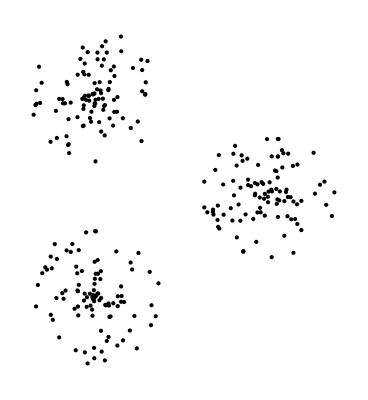

```mathematica
Graphics[Map[Point[#]&,Flatten[samples[3,"class"],1]]]
```

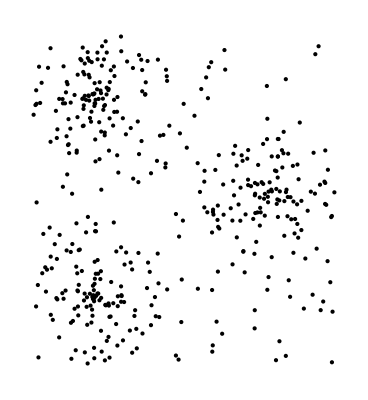

```mathematica
Graphics[Map[Point[#]&,Join[Flatten[samples[3,"class"],1],samples[3,"background"]]]]
```

```mathematica
samplesS[3]=ExportString[Join[Flatten[samples[3,"class"],1],samples[3,"background"]],"TSV"]<>"\n";
```

```mathematica
(*(samples[3,"All"]=Append[samples[3,"class"],samples[3,"background"]])//Length*)
```

全サンプルの平均半径

```mathematica
id=3
```

3

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{-0.0122606,0.00326999}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

1.01003

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{0.958673,0.0158914},{-0.500193,0.852192},{-0.495261,-0.858274}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{0.306362,0.275759,0.287733}

```mathematica
Export["data3.tsv",strDataToExportStr[3],"String"]
```

data3.tsv

```mathematica
Export["data3.ans.totalR",totalR[id],"Table"]
```

data3.ans.totalR

```mathematica
Export["data3.ans.clRs",clRs[id],"Table"]
```

data3.ans.clRs

## 3D

### data 7 (chain)

```mathematica
anntS[7]="Model: double chain.\n"
```

Model: double chain.

```mathematica
dim[7]=3;
numClass[7]=2;
numSample[7]={150,150};
numBG[7]={0};
```

```mathematica
dimS[7]=StringJoin[Riffle[{ToString[dim[7]],ToString[numClass[7]],ToString[numSample[7]],ToString[numBG[7]]},"\t"],"\n"]
```

3	2	{150, 150}	{0}

```mathematica
centers[7]={{0,0,0},{1,0,0}}
```

{{0,0,0},{1,0,0}}

```mathematica
(*origins[6]={{0,0},{0,0},{0,0}}*)
```

```mathematica
centersS[7]=ExportString[centers[7],"TSV"]<>"\n"
```

0	0	0
1	0	0

```mathematica
samples[7,1]=Map[sPolarToxyz[#]&,Table[{1,Pi/2,ph},{ph,0,2Pi-2Pi/150,2Pi/150}]];
```

```mathematica
Map[Point[#]&,samples[7,1]]//Length
```

150

```mathematica
Map[Point[#]&,samples[7,1]]//Graphics3D
```

-Graphics3D-

```mathematica
samples[7,2]=Map[sPolarToxyz[#]&,Table[{1,th,0},{th,0,2Pi-2Pi/150,2Pi/150}]];
```

```mathematica
Map[Point[#]&,samples[7,2]]//Length
```

150

```mathematica
Map[Point[#]&,samples[7,2]]//Graphics3D
```

-Graphics3D-

```mathematica
(*(samples[7,"All"]=Join[samples[7,1],Map[#+centers[7][[2]]&,samples[7,2]]]//N)//Length*)
```

```mathematica
(samples[7,"class"]=List[samples[7,1],Map[#+centers[7][[2]]&,samples[7,2]]]//N)//Length
```

2

```mathematica
Map[Point[#]&,samples[7,"class"]]//Graphics3D
```

-Graphics3D-

```mathematica
samplesS[7]=ExportString[Flatten[samples[7,"class"],1],"TSV"]<>"\n";
```

全サンプルの平均半径

```mathematica
id=7
```

7

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{0.5,-2.7293×10^-18,2.96059×10^-18}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

1.06354

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{5.92119×10^-18,-5.4586×10^-18,0.},{1.,0.,5.92119×10^-18}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{1.,1.}

```mathematica
Export["data7.tsv",strDataToExportStr[7],"String"]
```

data7.tsv

```mathematica
Export["data7.ans.totalR",totalR[id],"Table"]
```

data7.ans.totalR

```mathematica
Export["data7.ans.clRs",clRs[id],"Table"]
```

data7.ans.clRs

## Many class

### data 8 (4 classes)

```mathematica
anntS[8]="Model: central random , circles, one radius, 2d-4class.\n"
```

Model: central random , circles, one radius, 2d-4class.

```mathematica
dim[8]=2;
numClass[8]=4;
numSample[8]={100,100,100,100};
numBG[8]={0};
```

```mathematica
dimS[8]=StringJoin[Riffle[{ToString[dim[8]],ToString[numClass[8]],ToString[numSample[8]],ToString[numBG[8]]},"\t"],"\n"]
```

2	4	{100, 100, 100, 100}	{0}

```mathematica
centers[8]={{2,2},{2,-2},{-2,2},{-2,-2}}
```

{{2,2},{2,-2},{-2,2},{-2,-2}}

```mathematica
centersS[8]=ExportString[centers[8],"TSV"]<>"\n"
```

2	2
2	-2
-2	2
-2	-2

```mathematica
distMean[8]=Tr[Flatten[distanceMat[centers[8]]//N]]/(numClass[8]^2-numClass[8])
```

4.55228

```mathematica
samples[8,"class"]=Table[Map[#+centers[8][[n]]&,Table[polarToxy[{RandomReal[{0,distMean[8]/4}],RandomReal[{0,2Pi}]}],{numSample[8][[n]]}]],{n,numClass[8]}];
```

```mathematica
maxmin[8]=Map[{Max[#],Min[#]}&,Transpose[Flatten[samples[8,"class"],1]]]
```

{{3.09734,-3.06806},{3.0632,-3.09892}}

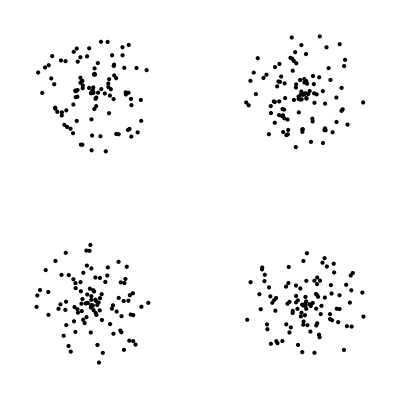

```mathematica
Graphics[Map[Point[#]&,Flatten[samples[8,"class"],1]]]
```

```mathematica
samplesS[8]=ExportString[Flatten[samples[8,"class"],1],"TSV"]<>"\n";
```

全サンプルの平均半径

```mathematica
id=8
```

8

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{-0.0188863,0.00661401}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

2.83927

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{1.89958,1.95443},{2.01542,-1.98778},{-1.99133,2.02047},{-1.99921,-1.96066}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{0.580362,0.569596,0.605452,0.559339}

```mathematica
Export["data8.tsv",strDataToExportStr[8],"String"]
```

data8.tsv

```mathematica
Export["data8.ans.totalR",totalR[id],"Table"]
```

data8.ans.totalR

```mathematica
Export["data8.ans.clRs",clRs[id],"Table"]
```

data8.ans.clRs

### data 9 (8 classes)

```mathematica
anntS[9]="Model: central random , circles, one radius, 2d-8class.\n"
```

Model: central random , circles, one radius, 2d-8class.

```mathematica
dim[9]=2;
numClass[9]=8;
numSample[9]={100,100,100,100,100,100,100,100};
numBG[9]={0};
```

```mathematica
dimS[9]=StringJoin[Riffle[{ToString[dim[9]],ToString[numClass[9]],ToString[numSample[9]],ToString[numBG[9]]},"\t"],"\n"]
```

2	8	{100, 100, 100, 100, 100, 100, 100, 100}	{0}

```mathematica
centers[9]={{7,7},{7,-7},{-7,7},{-7,-7},{0,20},{20,0},{0,-20},{-20,0}}
```

{{7,7},{7,-7},{-7,7},{-7,-7},{0,20},{20,0},{0,-20},{-20,0}}

```mathematica
centersS[9]=ExportString[centers[9],"TSV"]<>"\n"
```

7	7
7	-7
-7	7
-7	-7
0	20
20	0
0	-20
-20	0

```mathematica
distMean[9]=Tr[Flatten[distanceMat[centers[9]]//N]]/(numClass[9]^2-numClass[9])
```

22.4998

```mathematica
samples[9,"class"]=Table[Map[#+centers[9][[n]]&,Table[polarToxy[{RandomReal[{0,distMean[9]/4}],RandomReal[{0,2Pi}]}],{numSample[9][[n]]}]],{n,numClass[9]}];
```

```mathematica
maxmin[9]=Map[{Max[#],Min[#]}&,Transpose[Flatten[samples[9,"class"],1]]]
```

{{25.1741,-25.3215},{25.292,-25.4902}}

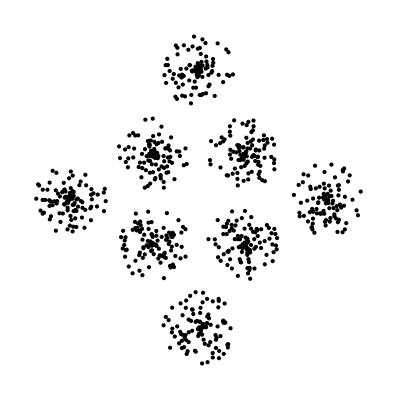

```mathematica
Graphics[Map[Point[#]&,Flatten[samples[9,"class"],1]]]
```

```mathematica
samplesS[9]=ExportString[Flatten[samples[9,"class"],1],"TSV"]<>"\n";
```

全サンプルの平均半径

```mathematica
id=9
```

9

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{-0.0344935,-0.0796514}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

15.1663

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{7.34916,7.18378},{7.16928,-6.8399},{-7.03234,6.68067},{-7.05337,-6.84649},{-0.463388,19.9275},{19.8137,-0.444655},{0.16319,-20.032},{-20.2222,-0.266176}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{2.8517,2.95616,2.62825,3.04195,2.65838,2.85259,3.11899,2.81984}

```mathematica
Export["data9.tsv",strDataToExportStr[9],"String"]
```

data9.tsv

```mathematica
Export["data9.ans.totalR",totalR[id],"Table"]
```

data9.ans.totalR

```mathematica
Export["data9.ans.clRs",clRs[id],"Table"]
```

data9.ans.clRs

### data 10 (3d-8 classes) (scale: base)

```mathematica
anntS[10]="Model: central random , circles, one radius, 3d-8class (base).\n"
```

Model: central random , circles, one radius, 3d-8class (base).

```mathematica
dim[10]=3;
numClass[10]=8;
numSample[10]={100,100,100,100,100,100,100,100};
numBG[10]={0};
```

```mathematica
dimS[10]=StringJoin[Riffle[{ToString[dim[10]],ToString[numClass[10]],ToString[numSample[10]],ToString[numBG[10]]},"\t"],"\n"]
```

3	8	{100, 100, 100, 100, 100, 100, 100, 100}	{0}

```mathematica
centers[10]=Tuples[{0,10},3]
```

{{0,0,0},{0,0,10},{0,10,0},{0,10,10},{10,0,0},{10,0,10},{10,10,0},{10,10,10}}

```mathematica
centersS[10]=ExportString[centers[10],"TSV"]<>"\n"
```

0	0	0
0	0	10
0	10	0
0	10	10
10	0	0
10	0	10
10	10	0
10	10	10

```mathematica
distMean[10]=Tr[Flatten[distanceMat[centers[10]]//N]]/(numClass[10]^2-numClass[10])
```

12.821

```mathematica
centers[10]
```

{{0,0,0},{0,0,10},{0,10,0},{0,10,10},{10,0,0},{10,0,10},{10,10,0},{10,10,10}}

```mathematica
samples[10,"class"]=Table[centers[10][[c]]+Table[RandomVariate[NormalDistribution[0,distMean[10]/16]],{3}],{c,numClass[10]},{100}];
```

```mathematica
maxmin[10]=Map[{Max[#],Min[#]}&,Transpose[Flatten[samples[10,"class"],1]]]
```

{{12.4781,-2.63907},{12.1012,-2.21408},{12.3111,-2.09692}}

```mathematica
Graphics3D[Map[Point[#]&,Flatten[samples[10,"class"],1]]]
```

-Graphics3D-

```mathematica
samplesS[10]=ExportString[Flatten[samples[10,"class"],1],"TSV"]<>"\n";
```

全サンプルの平均半径

```mathematica
id=10
```

10

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{4.99743,5.0067,4.98785}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

8.70997

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{0.0938159,-0.0816702,-0.000498069},{-0.0397888,0.0459709,10.1038},{0.118739,10.0249,-0.0435164},{-0.0735292,9.95421,10.0122},{9.91949,0.119042,-0.112416},{9.86653,0.0467694,9.87995},{10.0429,9.99588,0.0782226},{10.0513,9.94847,9.98505}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{1.40435,1.30547,1.26909,1.18767,1.23663,1.26906,1.19392,1.35993}

```mathematica
Export["data10.tsv",strDataToExportStr[10],"String"]
```

data10.tsv

```mathematica
Export["data10.ans.totalR",totalR[id],"Table"]
```

data10.ans.totalR

```mathematica
Export["data10.ans.clRs",clRs[id],"Table"]
```

data10.ans.clRs

### data 10.2 (3d-8 classes) (scale: 2)

```mathematica
anntS[10.2]="Model: central random , circles, one radius, 3d-8class, scaled.\n"
```

Model: central random , circles, one radius, 3d-8class, scaled.

```mathematica
dim[10.2]=3;
numClass[10.2]=8;
numSample[10.2]={100,100,100,100,100,100,100,100};
numBG[10.2]={0};
```

```mathematica
dimS[10.2]=StringJoin[Riffle[{ToString[dim[10.2]],ToString[numClass[10.2]],ToString[numSample[10.2]],ToString[numBG[10.2]]},"\t"],"\n"]
```

3	8	{100, 100, 100, 100, 100, 100, 100, 100}	{0}

```mathematica
centers[10.2]=Tuples[{0,10},3]/4//N
```

{{0.,0.,0.},{0.,0.,2.5},{0.,2.5,0.},{0.,2.5,2.5},{2.5,0.,0.},{2.5,0.,2.5},{2.5,2.5,0.},{2.5,2.5,2.5}}

```mathematica
centersS[10.2]=ExportString[centers[10.2],"TSV"]<>"\n";
```

```mathematica
distMean[10.2]=Tr[Flatten[distanceMat[centers[10.2]]//N]]/(numClass[10.2]^2-numClass[10.2])
```

3.20525

```mathematica
samples[10.2,"class"]=Table[centers[10.2][[c]]+Table[RandomVariate[NormalDistribution[0,distMean[10.2]/10]],{3}],{c,numClass[10.2]},{100}];
```

```mathematica
maxmin[10.2]=Map[{Max[#],Min[#]}&,Transpose[Flatten[samples[10.2,"class"],1]]]
```

{{3.69607,-0.859388},{3.42039,-1.04654},{3.31321,-0.944035}}

```mathematica
Graphics3D[Map[Point[#]&,Flatten[samples[10.2,"class"],1]]]
```

-Graphics3D-

```mathematica
samplesS[10.2]=ExportString[Flatten[samples[10.2,"class"],1],"TSV"]<>"\n";
```

全サンプルの平均半径

```mathematica
id=10.2
```

10.2

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{1.26425,1.25858,1.23261}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

2.20406

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{-0.00692272,0.0286025,0.0219271},{0.0846019,0.0121557,2.51476},{0.00880222,2.56588,-0.0182135},{0.0320471,2.55132,2.47632},{2.48,-0.0161748,-0.0119333},{2.53833,-0.0051417,2.46299},{2.50723,2.474,-0.0376221},{2.46992,2.45796,2.45264}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{0.51225,0.510695,0.477541,0.517048,0.55401,0.553418,0.526007,0.536271}

```mathematica
Export["data10-2.tsv",strDataToExportStr[10.2],"String"]
```

data10-2.tsv

```mathematica
Export["data10-2.ans.totalR",totalR[id],"Table"]
```

data10-2.ans.totalR

```mathematica
Export["data10-2.ans.clRs",clRs[id],"Table"]
```

data10-2.ans.clRs

### data 10.3 (3d-8 classes) (scale: 3)

```mathematica
anntS[10.3]="Model: central random , circles, one radius, 3d-8class, scaled(3).\n"
```

Model: central random , circles, one radius, 3d-8class, scaled(3).

```mathematica
dim[10.3]=3;
numClass[10.3]=8;
numSample[10.3]={100,100,100,100,100,100,100,100};
numBG[10.3]={0};
```

```mathematica
dimS[10.3]=StringJoin[Riffle[{ToString[dim[10.3]],ToString[numClass[10.3]],ToString[numSample[10.3]],ToString[numBG[10.3]]},"\t"],"\n"]
```

3	8	{100, 100, 100, 100, 100, 100, 100, 100}	{0}

```mathematica
centers[10.3]=Tuples[{0,10},3]/8//N
```

{{0.,0.,0.},{0.,0.,1.25},{0.,1.25,0.},{0.,1.25,1.25},{1.25,0.,0.},{1.25,0.,1.25},{1.25,1.25,0.},{1.25,1.25,1.25}}

```mathematica
centersS[10.3]=ExportString[centers[10.3],"TSV"]<>"\n"
```

0.	0.	0.
0.	0.	1.25
0.	1.25	0.
0.	1.25	1.25
1.25	0.	0.
1.25	0.	1.25
1.25	1.25	0.
1.25	1.25	1.25

```mathematica
distMean[10.3]=Tr[Flatten[distanceMat[centers[10.3]]//N]]/(numClass[10.3]^2-numClass[10.3])
```

1.60262

```mathematica
samples[10.3,"class"]=Table[centers[10.3][[c]]+Table[RandomVariate[NormalDistribution[0,distMean[10.3]/10]],{3}],{c,numClass[10.3]},{100}];
```

```mathematica
maxmin[10.3]=Map[{Max[#],Min[#]}&,Transpose[Flatten[samples[10.3,"class"],1]]]
```

{{1.70701,-0.411033},{1.72602,-0.372833},{1.68651,-0.511483}}

```mathematica
Graphics3D[Map[Point[#]&,Flatten[samples[10.3,"class"],1]]]
```

-Graphics3D-

```mathematica
samplesS[10.3]=ExportString[Flatten[samples[10.3,"class"],1],"TSV"]<>"\n";
```

全サンプルの平均半径

```mathematica
id=10.3
```

10.3

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{0.626292,0.62115,0.61758}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

1.09777

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{-0.0026431,0.0116823,-0.00460423},{-0.014372,0.0244711,1.25249},{0.0340663,1.22826,-0.0229324},{0.0171925,1.20873,1.25041},{1.24143,-0.000563676,0.00430137},{1.24858,0.00652472,1.24907},{1.2626,1.24197,-0.0343922},{1.22349,1.24812,1.2463}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{0.251641,0.244662,0.259205,0.266206,0.237913,0.247089,0.245332,0.254}

```mathematica
Export["data10-3.tsv",strDataToExportStr[10.3],"String"]
```

data10-3.tsv

```mathematica
Export["data10-3.ans.totalR",totalR[id],"Table"]
```

data10-3.ans.totalR

```mathematica
Export["data10-3.ans.clRs",clRs[id],"Table"]
```

data10-3.ans.clRs

### data 10.4 (3d-8 classes) (scale: 4)

```mathematica
id=10.4
```

10.4

```mathematica
anntS[id]="Model: central random , circles, one radius, 3d-8class, scaled(4).\n"
```

Model: central random , circles, one radius, 3d-8class, scaled(4).

```mathematica
dim[id]=3;
numClass[id]=8;
numSample[id]={100,100,100,100,100,100,100,100};
numBG[id]={0};
```

```mathematica
dimS[id]=StringJoin[Riffle[{ToString[dim[id]],ToString[numClass[id]],ToString[numSample[id]],ToString[numBG[id]]},"\t"],"\n"]
```

3	8	{100, 100, 100, 100, 100, 100, 100, 100}	{0}

```mathematica
centers[id]=Tuples[{0,10},3]/8//N
```

{{0.,0.,0.},{0.,0.,1.25},{0.,1.25,0.},{0.,1.25,1.25},{1.25,0.,0.},{1.25,0.,1.25},{1.25,1.25,0.},{1.25,1.25,1.25}}

```mathematica
centersS[id]=ExportString[centers[id],"TSV"]<>"\n"
```

0.	0.	0.
0.	0.	1.25
0.	1.25	0.
0.	1.25	1.25
1.25	0.	0.
1.25	0.	1.25
1.25	1.25	0.
1.25	1.25	1.25

```mathematica
distMean[id]=Tr[Flatten[distanceMat[centers[id]]//N]]/(numClass[id]^2-numClass[id])
```

1.60262

```mathematica
samples[id,"class"]=Table[centers[id][[c]]+Table[RandomVariate[NormalDistribution[0,distMean[id]/15]],{3}],{c,numClass[id]},{100}];
```

```mathematica
maxmin[id]=Map[{Max[#],Min[#]}&,Transpose[Flatten[samples[id,"class"],1]]]
```

{{1.55564,-0.329503},{1.56783,-0.340569},{1.56548,-0.296105}}

```mathematica
Graphics3D[Map[Point[#]&,Flatten[samples[id,"class"],1]]]
```

-Graphics3D-

```mathematica
samplesS[id]=ExportString[Flatten[samples[id,"class"],1],"TSV"]<>"\n";
```

全サンプルの平均半径

```mathematica
id=10.4
```

10.4

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{0.630253,0.62393,0.628209}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

1.09344

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{0.0090846,-0.00812739,-0.00634306},{0.0185209,-0.00244912,1.24794},{0.000341128,1.25142,0.000588511},{0.00678289,1.25801,1.26689},{1.26112,-0.0127636,0.00262348},{1.24679,0.0211539,1.2642},{1.23918,1.23068,-0.00178255},{1.2602,1.25353,1.25155}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{0.1725,0.172952,0.172013,0.161025,0.169512,0.167442,0.170725,0.167981}

```mathematica
Export["data10-4.tsv",strDataToExportStr[id],"String"]
```

data10-4.tsv

```mathematica
Export["data10-4.ans.totalR",totalR[id],"Table"]
```

data10-4.ans.totalR

```mathematica
Export["data10-4.ans.clRs",clRs[id],"Table"]
```

data10-4.ans.clRs

## high Dimensional

## Experimental